```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
l=Flatten@Import["sum.dat"];
cnt=Import["cnt","Table"][[1,1]];
l=l/cnt;
l=Rest[l];
len=Length[l];
```

```mathematica
f=Union@Floor@Table[1.1^p,{p,1,130}];avg=Table[{(f[[i]]+f[[i+1]])/2.,Mean[Take[l,{f[[i]],f[[i+1]]}]]},{i,Length[f]-1}];
p1=ListLogLogPlot[avg,PlotStyle->Red,Joined->True];
p2=ListLogLogPlot[l,PlotRange->All];
Show[p2,p1];
```

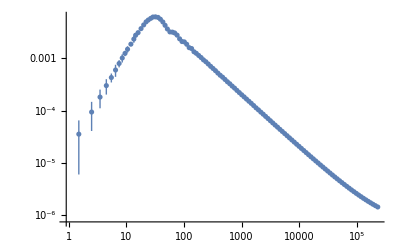

```mathematica
avgerr=Table[{(f[[i]]+f[[i+1]])/2.,Around[Mean[Take[l,{f[[i]],f[[i+1]]}]],StandardDeviation[Take[l,{f[[i]],f[[i+1]]}]]/Sqrt[f[[i+1]]-f[[i]]]]},{i,Length[f]-1}];
ListLogLogPlot[avgerr]
```

```mathematica
Export["spectrum.dat",avg]
```

spectrum.dat